```mathematica
Verlet[m_,x0_,v0_,F_,dt_,Ns_] := Module[{xout,xnext, xcur,xprev,t,index},
xout = Table[0.0,{j,1,Ns}];
xcur = x0;
xprev = x0 - dt v0 +(1/2) F[x0,0.0]/m dt^2;
t = 0.0;
xout[[1]] = {t,x0};
For[index = 2, index ≤ Ns, index=index+1,
xnext = 2.0 xcur - xprev + dt^2 F[xcur, t]/m;
t = t + dt;
xout[[index]] = {t, xnext};
xprev = xcur;
xcur = xnext;
];
Return[xout];
]
```

```mathematica
Fgrav[x_,t_] := -m g
```

```mathematica
m = 1.0;
g = 9.8;
```

```mathematica
test = Verlet[m,1.0,0.0,Fgrav, .01,50];
```

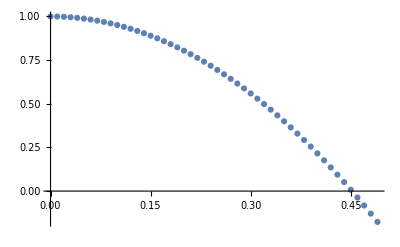

```mathematica
G0 = ListPlot[test]
```

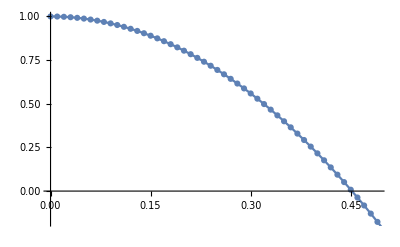

```mathematica
G1= Plot[-1/2 g t^2 + 1.,{t,0,.5}];
Show[G0,G1]
```

#### 2.1

```mathematica
k = 4;
```

```mathematica
F[x_,t_] := -k x
```

```mathematica
springVerlet = Verlet[1, 2,0, F, 4 Pi/1000, 1000];
```

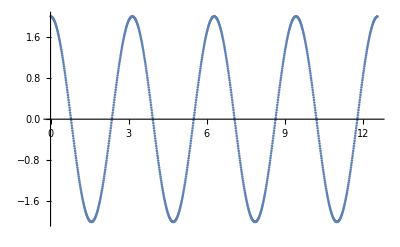

```mathematica
ListPlot[springVerlet]
```

```mathematica
springActualFunc[t_] := 2 Cos[2 t]
```

```mathematica
springActual = Table[{t,springActualFunc[t]}, {t, 0, 4 Pi, 4 Pi/1000}];
```

```mathematica
springResiduals = Table[{springVerlet[[i]][[1]], springVerlet[[i]][[2]]-springActual[[i]][[2]]}, {i, 1, Length[springVerlet]}];
```

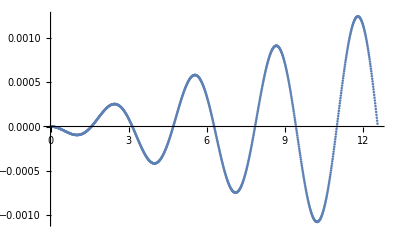

```mathematica
ListPlot[springResiduals]
```

#### 2.2

The "force" in this problem is actually the torque, since we have θ instead of x. However, because the mass at the end of the cable is 1kg and the length of the cable is 1kg, the “force” is given by

```mathematica
ℓ = 1;
```

```mathematica
pendulumForce[θ_,t_] := (-g/ℓ) Sin[θ]
```

```mathematica
pendulumLinearFunc[θInit_, t_] := θInit Cos[Sqrt[g/ℓ] t];
```

The angles we want to work with are

```mathematica
angles = {10°, 45°, 80°};
```

Then, for each angle we have:

10 °

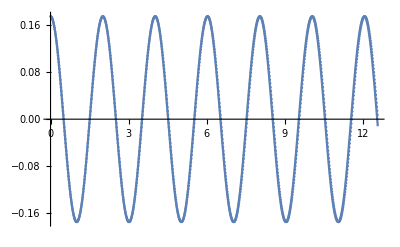

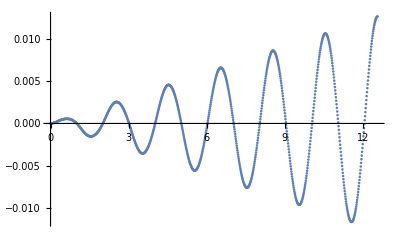

45 °

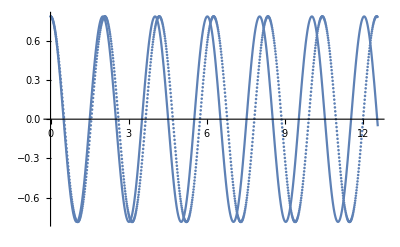

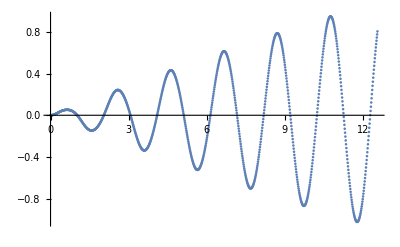

80 °

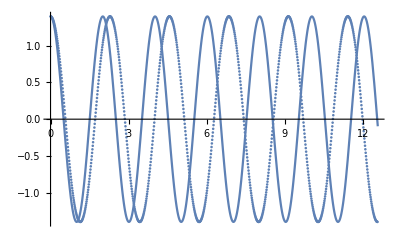

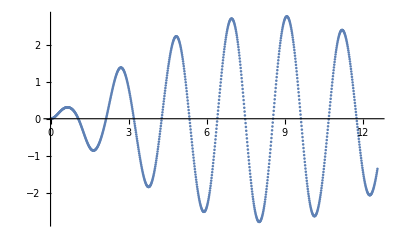

```mathematica
Do[
Print[θInitial];
verletPendulum = Verlet[1, θInitial, 0, pendulumForce, 4 Pi / 1000, 1000];
Print[Show[ListPlot[verletPendulum], Plot[pendulumLinearFunc[θInitial, θ], {θ,0,4Pi}]]];
pendulumResiduals = Table[{verletPendulum[[i]][[1]], verletPendulum[[i]][[2]] - pendulumLinearFunc[θInitial,verletPendulum[[i]][[1]]]}, 
{i, 1, Length[verletPendulum]}];
(*Print[pendulumResiduals]*);
Print[ListPlot[pendulumResiduals]];

,{θInitial, angles}]
```

#### 2.3

```mathematica
c = 3 10^8
```

300000000

```mathematica
VerletRelativistic[m_,x0_,v0_,F_,dt_,Ns_] := 
Module[{xout,xnext, xcur,xprev,vcur,t,index},
xout = Table[0.0,{j,1,Ns}];
xcur = x0;
xprev = x0 - dt v0 +(1/2) F[x0,0.0]/m dt^2;
t = 0.0;
vcur = v0;
xout[[1]] = {t,x0};
For[index = 2, index ≤ Ns, index=index+1,
xnext = 2.0 xcur - xprev + dt^2 F[xcur, t](1-(vcur/c)^2)^(3/2)/m;
t = t + dt;
xout[[index]] = {t, xnext};
xprev = xcur;
xcur = xnext;
vcur = (xcur-xprev)/dt + dt F[xcur,t] (1-(vcur/c)^2)^(3/2)/m;
];
Return[xout];
]
```

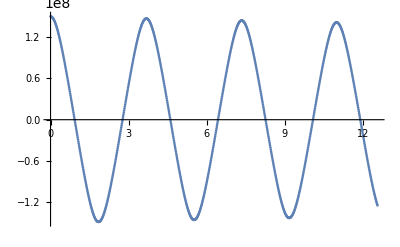

```mathematica
relSpringVerlet = VerletRelativistic[1, c /2,0, F, 4 Pi/1000, 1000];
ListPlot[relSpringVerlet]
```

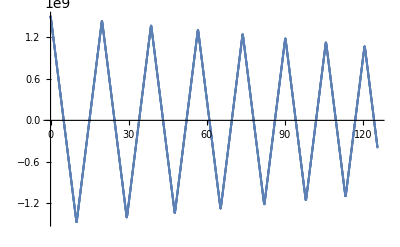

```mathematica
relSpringVerlet2 = VerletRelativistic[1, 5c,0, F,4 Pi/1000, 10000];
ListPlot[relSpringVerlet2]
```

This function is what we expect, since its velocity is capped out at c for nearly its whole travel. It has a period of about 19s.

```mathematica
VerletWithVelocity[m_,x0_,v0_,F_,dt_,Ns_] := Module[{xout,xnext, xcur,xprev,vcur,t,index},
xout = Table[0.0,{j,1,Ns}];
xcur = x0;
xprev = x0 - dt v0 +(1/2) F[x0,v0,0.0]/m dt^2;
t = 0.0;
vcur = v0;
xout[[1]] = {t,x0};
For[index = 2, index ≤ Ns, index=index+1,
xnext = 2.0 xcur - xprev + dt^2 F[xcur,vcur, t]/m;
t = t + dt;
xout[[index]] = {t, xnext};
xprev = xcur;
xcur = xnext;
vcur = (xcur-xprev)/dt + dt F[xcur,vcur,t]/m;
];
Return[xout];
]
```

An arbitrary damping parameter:

```mathematica
b = 0.2
```

0.2

```mathematica
DampedSpringF[x_,v_,t_] := -k x - 2 m b v;
```

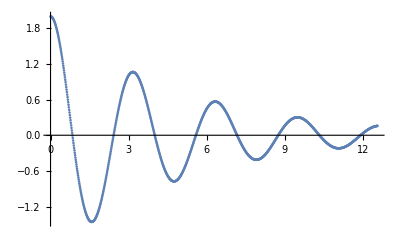

```mathematica
ListPlot[VerletWithVelocity[1,2,0, DampedSpringF, 4 Pi/1000, 1000]]
```

```mathematica
xoutDump = Table[0.0, {i, 1, 1000}];
```

```mathematica
VerletWithVelocityRelativity[m_,x0_,v0_,F_,dt_,Ns_] := 
Module[{xout,xnext, xcur,xprev,vcur,t,index, tmp},
xout = Table[0.0,{j,1,Ns}];
xcur = x0;
vcur = v0;
xprev = x0 - dt v0 +(1/2) F[x0,vcur,0.0](1-(vcur/c)^2)^(3/2)/m dt^2;
t = 0.0;
xout[[1]] = {t,x0};
For[index = 2, index ≤ Ns, index=index+1,
xnext = 2.0 xcur - xprev + dt^2 F[xcur,vcur, t](1-(vcur/c)^2)^(3/2)/m;
t = t + dt;
xout[[index]] = {t, xnext};
xprev = xcur;
xcur = xnext;
tmp = (xcur-xprev)/dt + dt F[xcur,vcur,t] (1-(vcur/c)^2)^(3/2)/m;
vcur = tmp;
xoutDump = xout;
];
Return[xout];
]
```

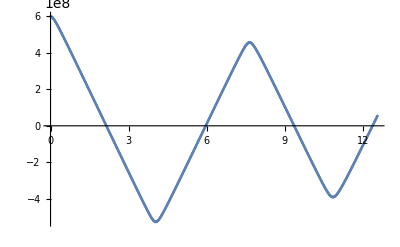

```mathematica
relSpringVerletDamped = VerletWithVelocityRelativity[1, 2c,0, DampedSpringF,4 Pi/1000, 1000];
ListPlot[relSpringVerletDamped]
```